# Метод на хордите

## Задача 1:

Задача: Дадено е уравенението:
x^2+  px − (q + 50) cos x − 2(p + q) = 0, където p и q са съответно предпоследната и последната цифра от факултетния ни номер (в случая p = 0 а q = 8)
x^2 + x − 58 cos x − 16 = 0
	 1.  Да се намери общия брой на корените на уравнението.
2. Да се локализира най-големия реален корен в интервала [a, b]. 
3. Да се проверят условията за приложение на метода на хордите.
		- проверка на сходимост
		- избор на начално приближение и постоянна точка
		- итерациите
	 4.  Да се изчисли корена по метода на хордите с точност 10^-4. Представете таблица с изчисленията.
	 5.  Да се провери колко итерации биха били необходими, ако се използва метода на разполовяването в същия интервал [a, b] за същата точност.
6.  Да се направи сравнение кой метод е по-ефективен за избрания интервал.

```mathematica
f[x_] := x^2 +x - 58 Cos[x] - 16
```

```mathematica
f[x]
```

8-x^2-(9 x)/(9+x^2)+Sin[x]

## 1. Да се намери общия брой на корените на уравнението

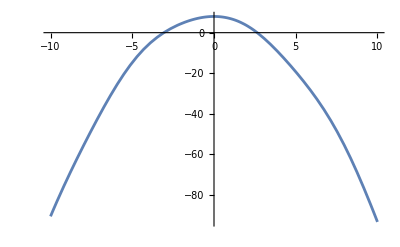

```mathematica
Plot[f[x], {x, -10, 10}]
```

Брой корени: 2

## 2. Да се локализира най-големия реален корен в интервала [a, b]

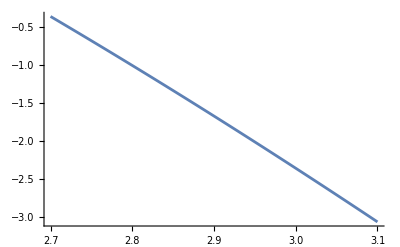

```mathematica
Plot[f[x], {x, 2.7, 3.1}]
```

```mathematica
f[2.7]
```

-8.48023

```mathematica
f[3.1]
```

-3.06761

Извод:
(1) Функцията е непрекъсната, защото е сума от непрекъснати функции (полином и синус).
(2) f(5) = -8.48023 ... < 0
       f(7) = -3.06761 ... < 0

## 3. Да се проверят условията за приложение на метода на хордите

### Проверка на сходимост

#### Графика на първата производна

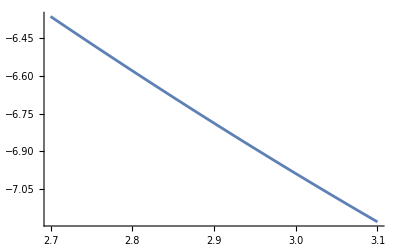

```mathematica
Plot[f'[x],{x,2.7,3.1}]
```

Извод: (1) Стойностите на първата производна в разглеждания интервал [2.7,3.1] са между -6.3 и -7.2. Следователно първата f'(x) > 0 в целия разглеждан интервал [2.7,3.1].

#### Графика на втората производна

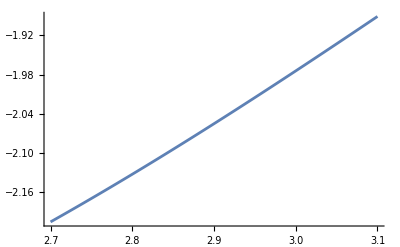

```mathematica
Plot[f''[x],{x,2.7,3.1}]
```

Извод : (2) Стойностите на втората производна в разглеждания интервал [2.7,3.1] са между -1.9 и -2.2. Следователно втората f'' (x) > 0 в целия разглеждан интервал [] .

Извод: От (1) и (2) следва, че първата и втората производна имат постоянни знаци в разглеждания интервал [2.7,3.1]. Следователно условията за сходимост на метода на хордите са изпълнени.

### Избор на начално приближение и постоянна точка

Нужно е да е изпълнено условието f(x0).f’’(x) < 0
В нашия случай f’’(x) >0. Следователно е нужно f(x0) <0

```mathematica
p = 2.7
```

2.7

```mathematica
x0 = 3.1
```

3.1

### Итериране

```mathematica
For[n = 0, n <= 10, n++,
x1 = x0 - f[x0]/(f[x0] - f[p])*(x0 - p);
Print["n = ",n,  " x_n = ", x1];
x0 = x1
]
```

n = 0 x_n = 2.64776

n = 1 x_n = 2.64379

n = 2 x_n = 2.64375

n = 3 x_n = 2.64375

n = 4 x_n = 2.64375

n = 5 x_n = 2.64375

n = 6 x_n = 2.64375

n = 7 x_n = 2.64375

n = 8 x_n = 2.64375

n = 9 x_n = 2.64375

n = 10 x_n = 2.64375

## 4. Да се изчисли корена по метода на хордите с точност 10^-4

### Изчисляване на постоянните величини

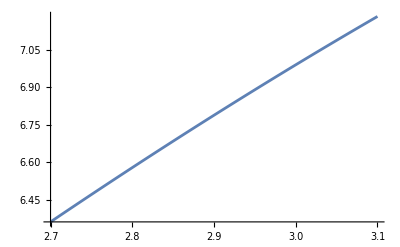

```mathematica
Plot[Abs[f'[x]],{x,2.7,3.1}]
```

От геометрично съображение минимума на абсолютната стойност на първата производна се достига в левия край на интервала, а максимума - в десния.

```mathematica
M1 = Abs[f'[2.7]]
```

6.36207

```mathematica
m1 = Abs[f'[3.1]]
```

7.18328

```mathematica
R = (M1 - m1)/m1
```

-0.182644

```mathematica
f[x_] := x^2 +x - 58 Cos[x] - 16
p = 2.7; x0 = 3.1;
M1 = Abs[f'[2.7]];
m1 = Abs[f'[3.1]];
R = (M1 - m1)/m1;
For[n = 0, n <= 10, n++,
x1 = x0 - f[x0]/(f[x0] - f[p])*(x0 - p);
Print["n = ",n,  " x_n = ", x1, " f(x_n) = ", f[x1], " ε_n = ", eps = R * Abs[x1 - x0]];
x0 = x1
]
```

n = 0 x_n = 0.444565 f(x_n) = -67.7201 ε_n = 5.96094

n = 1 x_n = 1.78266 f(x_n) = 1.15674 ε_n = 3.00376

n = 2 x_n = 1.75922 f(x_n) = -0.282088 ε_n = 0.0526187

n = 3 x_n = 1.7649 f(x_n) = 0.0671473 ε_n = 0.0127544

n = 4 x_n = 1.76354 f(x_n) = -0.0160774 ε_n = 0.00304041

n = 5 x_n = 1.76387 f(x_n) = 0.00384412 ε_n = 0.000727727

n = 6 x_n = 1.76379 f(x_n) = -0.00091944 ε_n = 0.000174015

n = 7 x_n = 1.76381 f(x_n) = 0.000219895 ε_n = 0.0000416201

n = 8 x_n = 1.76381 f(x_n) = -0.0000525914 ε_n = 9.95398×10^-6

n = 9 x_n = 1.76381 f(x_n) = 0.000012578 ε_n = 2.38065×10^-6

n = 10 x_n = 1.76381 f(x_n) = -3.00823×10^-6 ε_n = 5.69369×10^-7

Цикъл със стоп-критерий при определена точност (в случая ε_n  = 0.0001)

```mathematica
f[x_] := x^2 +x - 58 Cos[x] - 16
p = 2.7; x0 = 3.1;
M1 = Abs[f'[2.7]];
m1 = Abs[f'[3.1]];
R = (M1 - m1)/m1;
epszad = 0.0001;
eps = 1;
Print["n = ",0,  " x_n = ", x0, " f(x_n) = ", f[x0]];
For[n = 1, eps > epszad, n++,
x1 = x0 - f[x0]/(f[x0] - f[p])*(x0 - p);
Print["n = ",n,  " x_n = ", x1, " f(x_n) = ", f[x1], " ε_n = ", eps = R * Abs[x1 - x0]];
x0 = x1
]
```

n = 0 x_n = 7.3 f(x_n) = 9.55143

n = 1 x_n = 7.14109 f(x_n) = -0.451213 ε_n = -0.0290241

## 5. Да се провери колко итерации биха били необходими, ако се използва метода на разполовяването в същия интервал [a, b] за същата точност.

```mathematica
Log2[(3.1 - 2.7)/0.0001] - 1
```

10.9658

## 6. Да се направи сравнение кой метод е по-ефективен за избрания интервал

Извод: По метода на разполовяването биха били необходими 11 итерации за достигане на исканата точност. А по метода на хордите беше необходима само 1 итерация. Следователно методът на хордите е по-ефективен за избрания интервал [2.7,3.1].

## Задача 2:

Задача: Дадено е уравенението:
(√(x^3) - (1 + p + q) * sin(x))/(1 + cos^2(x)), където p и q са съответно предпоследната и последната цифра от факултетния ни номер (в случая p = 0 а q = 8)
(√(x^3) - 9* sin(x))/(1 + cos^2(x))
	 1.  Да се намери общия брой на корените на уравнението.
2. Да се локализира най-малкия реален корен в интервала [a, b]. 
3. Да се проверят условията за приложение на метода на хордите.
	         - проверка на сходимост
		- избор на начално приближение и постоянна точка
		- итерациите
	 4.  Да се изчисли корена по метода на хордите с точност 0,000001. Представете таблица с изчисленията.
	 5.  Да се провери колко итерации биха били необходими, ако се използва метода на разполовяването в същия интервал [a, b] за същата точност.
6.  Да се направи сравнение кой метод е по-ефективен за избрания интервал.

```mathematica
f[x_] := (√(x^3)-9)/(2 - Sin[x])
```

```mathematica
f[x]
```

(-9+√(x^3))/(2-Sin[x])

## 1. Да се намери общия брой на корените на уравнението

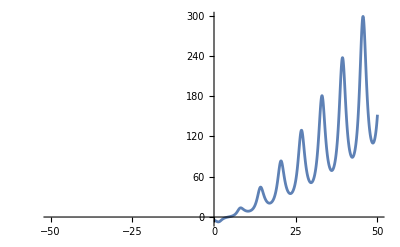

```mathematica
Plot[f[x], {x, -50, 50}]
```

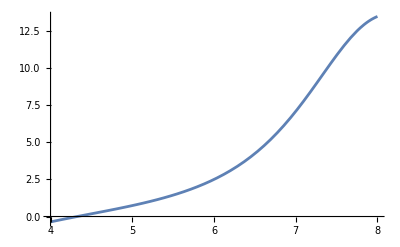

```mathematica
Plot[f[x], {x, 4, 8}]
```

Брой корени: 1

## 2. Да се локализира най-малкия реален корен в интервала [a, b]

```mathematica
Plot[f[x], {x, 4, 8}]
```

-Graphics-

```mathematica
f[4.]
```

-0.362739

```mathematica
f[8.]
```

13.4839

Извод:
(1) Функцията е непрекъсната, защото е сума от непрекъснати функции.
(2) f(5) = -0.362739 < 0
       f(7) = 13.4839 > 0
       => Функцията има различни знаци в двата края на разглеждания интервал [4; 8].
       От (1) и (2) следва, че функцията има поне един корен в разглеждания интервал [4; 8].

## 3. Да се проверят условията за приложение на метода на хордите

### Проверка на сходимост

#### Графика на първата производна

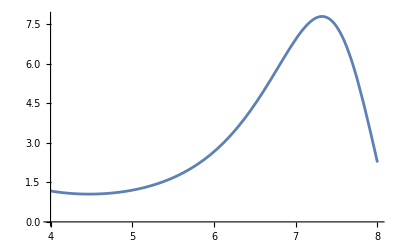

```mathematica
Plot[f'[x],{x,4,8}]
```

Извод: (1) Стойностите на първата производна в разглеждания интервал [4; 8] са между 1 и 7.8 Следователно първата f'(x) > 0 в целия разглеждан интервал [4; 8].

#### Графика на втората производна

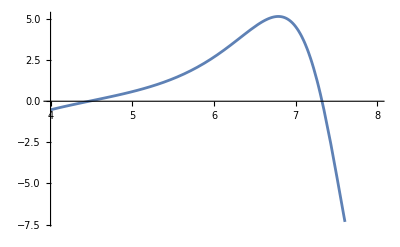

```mathematica
Plot[f''[x],{x,4,8}]
```

Извод : (2) Стойностите на втората производна в разглеждания интервал [4; 8] са между -0.5 и -7. Следователно втората производна няма постоянна стойност в разглеждания интервал [4, 8] .